# Report Project X

Course code: IX1501
Date: 2019-09-08

Viktor Jäger, vjager@kth.se
Sam Florin, sflorin@kth.se

Task: Winning a Teddy

## Summery

### Task

At a dice game you throw five dice in the form of the Platonic Solids. The dice are numbered with integers 1,2,…,n where n is the number of sides. The tetrahedron has its result number (1-4) written at the vertex pointing up. All other bodies have the result number on the side facing up. 
-Graphics-
At a fun-fair you can win a giant Teddy bear if you participate in the mentioned dice game. You invest €2 and then throw the five dice. If the sum S satisfies S≤10 or S≥45 you will win the Teddy. The following problems are expected to be solved by using convolution.

- Determine the exact probability function of the sum.
- Determine the exact probability of winning the Teddy prize. Also give a floating point answer.
- Determine the expected investment to win a Teddy.
- The probability of winning (at least one) Teddy if you play twenty times?

### Result

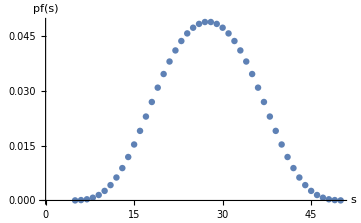
The probability function sum is determined by the probability function convolution of the individual dices.
pfSum(x)=pfd4(x)*pfd6(x)*pfd8(x)*pfd12(x)*pfd20(x) , 
where '*’ denotes convolution. The graph illustrates the probability function as a function of the five dices sum for a single dice roll.

   	-Graphics-
   	
 Determine the exact probability of winning the Teddy prize. Also give a floating point answer.
 The probability of  rolling correct sum is: 
P(S=s), 5 ≤ s ≤ 10 ∧ 45 ≥ s ≥ 50
 P(S={5 ≤ s ≤ 10 })+P(S={45 ≥ s ≥ 50})= 41/3840=1,06771..%
 Determine the expected investment to win a Teddy.
 After how many times you are expected to win a Teddy is: 
1/(41/3840)=187.317
 Since the problem is Discrete we round off to 188. The roll costs 2£ which gives the investment:
188*2=376£
What’s the probability of winning (at least one) Teddy if you play twenty times?
41/3840*20=41/192=0.213542=21,3542%

## Method

### Probability function of the sum

Variables p_Xd4 - p_Xd20 are the probability functions of each individual dice. The five dices makes up the probability space: Ω={5≤x≤50}. This space has a finite set, function is discrete.

p_Xd4=ConstantArray[1,4]/4;
P_Xd6=ConstantArray[1,6]/6;
P_Xd8=ConstantArray[1,8]/8;
P_Xd12=ConstantArray[1,12]/12;
p_Xd20=ConstantArray[1,20]/20;

Variables p_Xd46 - P_Xsum which is the result functions of how one function is modified by the other ending up with P_Xsum.

p_Xd46=ListConvolve[d4,d6,{1,-1},0];
P_Xd812=ListConvolve[d8,d12,{1,-1},0];
P_Xd46812=ListConvolve[pfd4d6,pfd8d12,{1,-1},0];
P_Xsum=ListConvolve[pfd4d6d8d12,d20,{1,-1},0]

Graph showing the probability distribution for the function of the sum.

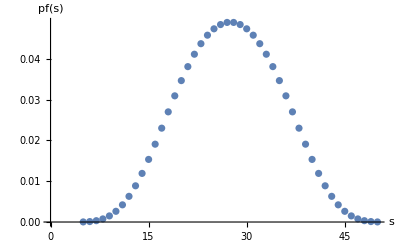

### Probability of winning the Teddy

The probability of winning a Teddy can be derived from the probability function. P(X=x), where 5≤x≤10 ∧ 45≤x≤50 gives the probability of winning.

P1=Total[Part[P_Xsum,1;;6]]
P2=Total[Part[P_Xsum,41;;46]]

The sum of the intervals P1 and P2 gives the total probability of winning.

P1uP2 = p1 + p2
N[P1uP2];
PercentForm[N[P1uP2]];

### Expected Investment

Expected win, we use the distribution function ‘för-första-gången-fördelning’ which tries until the first time result. 
Definition: p_X(k)=(1-p)^(k-1)p, k=1,2,..., where 0<p is said to be 'för-första-gången-fördelad'

expectedWin=1/P1uP2

Expected investment with cost 2£:

expectedInvestment=expectedWin*2 //N

### Probability of winning with 20 attempts

Probability of winning with 20 rolls:

1-(1-P1uP2)^20//N

## Code

```mathematica
Subscript[p, Xd4]=ConstantArray[1,4]/4;
Subscript[P, Xd6]=ConstantArray[1,6]/6;
Subscript[P, Xd8]=ConstantArray[1,8]/8;
Subscript[P, Xd12]=ConstantArray[1,12]/12;
Subscript[p, Xd20]=ConstantArray[1,20]/20;
```

```mathematica
Subscript[p, Xd46]=ListConvolve[d4,d6,{1,-1},0];
Subscript[P, Xd812]=ListConvolve[d8,d12,{1,-1},0];
Subscript[P, Xd46812]=ListConvolve[pfd4d6,pfd8d12,{1,-1},0];
Subscript[P, Xsum]=ListConvolve[pfd4d6d8d12,d20,{1,-1},0]
```

{1/46080,1/9216,1/3072,7/9216,23/15360,121/46080,97/23040,29/4608,409/46080,61/5120,707/46080,293/15360,53/2304,311/11520,95/3072,1597/46080,39/1024,379/9216,1007/23040,211/4608,1091/23040,223/4608,1127/23040,1127/23040,223/4608,1091/23040,211/4608,1007/23040,379/9216,39/1024,1597/46080,95/3072,311/11520,53/2304,293/15360,707/46080,61/5120,409/46080,29/4608,97/23040,121/46080,23/15360,7/9216,1/3072,1/9216,1/46080}

```mathematica
ListPlot[{Range[5,50],Subscript[P, Xsum]}//Transpose,AxesLabel->{"s","pf(s)"}]
```

-Graphics-

```mathematica
P1=Total[Part[Subscript[P, Xsum],1;;6]]
P2=Total[Part[Subscript[P, Xsum],41;;]]
```

41/7680

41/7680

```mathematica
P1uP2=P1+P2
N[P1uP2]
PercentForm[N[P1uP2]]
```

41/3840

0.0106771

PercentForm[0.0106771]

```mathematica
expectedWin=1/P1uP2
```

3840/41

```mathematica
expectedInvestment=expectedWin*2
```

```mathematica
41/3840*20 //N
```

0.213542

```mathematica
1-(1-P1uP2)^20//N
```

0.193208